# Name | M# |

The standard ODE model for mixing in tanks is common sense not rocket science!
 https://xkcd.com/2974/

```mathematica
Graphics3D[ {EdgeForm[Thick],
{Blue,Cylinder[{{0,0,0},{0,0,1}},1]},
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,1.5}},1.02]},
Text["Capacity             |     | L       
 Vol @ t=0          |            | L       
Conc @ t=0       |        | g/L",Background->White]
},
Boxed->False,
PlotLabel->"Tank_",
DisplayFunction->CreateDocument
]
```

-Graphics3D-

```mathematica
?Tube
```

```mathematica
?Tube
```

```mathematica
?CapForm
```

```mathematica
Graphics3D[{
{CapForm[None],Tube[{{0,0,0},{10,0,0}},0.2]},
{Text[" ⟶     L/s",{5,0,0},Background->White]}
},
PlotRange->All,
Boxed->False]
Graphics3D[{
{CapForm[None],Tube[{{0,0,0},{10,0,0}},0.2]},
{Text[" ⟵     L/s",{5,0,0},Background->White]}
},
PlotRange->All,
Boxed->False]

Graphics3D[{
{CapForm[None],Tube[{{0,0,0},{5,0,0},{0,5,5}},0.2]},
{Text[" ⟵     L/s",{5,0,0},Background->White]}
},
PlotRange->All,
Boxed->False]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
?DisplayFunction
```

```mathematica
Options[Text]
```

{Background→None,BaseStyle→{},ContentSelectable→Automatic,FormatType:>Automatic}

```mathematica
GraphPlot3D[CompleteGraph[4,DirectedEdges->True,EdgeLabels->Automatic],
BoxRatios->{1,1,1},
Boxed->True,
Axes->True]
```

-Graphics3D-

Write down, simulate and plot the solution of the standard ODE model for the well mixed tank problem shown below.

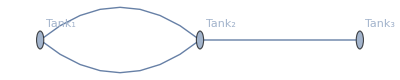

```mathematica
GraphPlot[{Subscript[Tank, 1]->Subscript[Tank, 2],Subscript[Tank, 2]->Subscript[Tank, 1],Subscript[Tank, 2]->Subscript[Tank, 3]},
VertexLabels->Automatic]
```